## MODELAGEM DA DINÂMICA PLANA DE AERONAVE SUPERSÔNICA DE PASSAGEIROS DURANTE FASE DE FREE-ROLL DA ATERRISSAGEM

## PME3380 - Modelagem de Sistemas Dinâmicos Prof. Dr. Agenor de Toledo Fleury Prof. Dr. Renato Maia Matarazzo Orsino

## Grupo K Lucas Retore Carboni - 12676091 Roberto Tetsuo Hamaoka - 10334770 Vitor Lucas Buter - 12555700

## Modelo principal - toque e free-roll

O equacionamento é baseado no seguinte modelo físico:
-Graphics-

e  são definidos como variáveis incrementais a partir da posição de equilíbrio dinâmico do avião transladando em pista plana com velocidade constante (M.R.U)
Importando as funções necessárias ao código

```mathematica
SetDirectory @ NotebookDirectory[];
<<Linearize.m
```

As coordenadas generalizadas são definidas como:

```mathematica
𝕢[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t]};
𝕧[t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]}; 
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = { Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, 𝕧[t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
α = 𝕢[t][[3]] + Subscript[Φ, 0];
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, PO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor P-O*)
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(𝕢[t][[3]] + Subscript[Φ, 0])], Subscript[D, GO]*Sin[(𝕢[t][[3]] + Subscript[Φ, 0])], 0}; (*Vetor G-O*)
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
D[Subscript[H, o], t] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[𝕧[t][[1]], t]) + Subscript[k, r]*(𝕢[t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(𝕢[t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) - Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) - Subscript[L, ext][[2]]//FullSimplify;
```

### O espaço de estados

```mathematica
DIN = {Subscript[TMB, m], Subscript[TMB, M], TQMA};

Sol[t_] = Flatten @ Solve[
	(# == 0)& /@ DIN,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;

𝕩[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
F = (𝕩'[t] /.Sol[t]); 
F //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
-(M Cos[Φ_0+θ[t]] D_GO^2 (2 g M Cos[Φ_0+θ[t]]+Sin[Φ_0+θ[t]] (-2 g M+S ρ C_L (u_longit+u_vento)^2) μ_rol)+1/2 M D_GO (-S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2+4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2)+J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(2 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(Sec[Φ_0+θ[t]] (-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D Tan[Φ_0+θ[t]])+2 M Sin[Φ_0+θ[t]] D_GO^2 θ'[t]^2+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])+2 (g M-g M μ_rol Tan[Φ_0+θ[t]]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t])))))/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz))

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
POSequi = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINlin = Linearize[DIN, POSequi]; (*ELS -> Equação dinâmica não-linear*)

Sollin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINlin,
	𝕧'[t]
	] // Collect[#, 𝕧[t], FullSimplify]&;
	
Subscript[𝕩, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[F, lin] = (Subscript[𝕩, lin]'[t] /.Sollin[t]);
Subscript[F, lin] //TrigReduce //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(2 M Cos[Φ_0] D_GO^2 ((2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t])+2 g M (-Cos[Φ_0]+Sin[Φ_0] θ[t]))+2 M S ρ Cos[Φ_0] D_GO D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))-2 J_oz (S ρ C_L (u_longit+u_vento)^2+2 k_t (q_1[t]-q_2[t])+2 c_t (q_1'[t]-q_2'[t])))/(4 M (M Cos[Φ_0]^2 D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (Cos[Φ_0] (C_L+C_D θ[t])+Sin[Φ_0] (C_D-C_L θ[t]))+D_GO (-2 g M Sin[Φ_0] (μ_rol+θ[t])+S ρ C_L (u_longit+u_vento)^2 (Cos[Φ_0]+μ_rol (Sin[Φ_0]+Cos[Φ_0] θ[t]))+2 Cos[Φ_0] (g M-g M μ_rol θ[t]+k_t (q_1[t]-q_2[t])+c_t (q_1'[t]-q_2'[t]))))/(2 M Cos[Φ_0]^2 D_GO^2-2 J_oz))

```mathematica
rep = {Subscript[C, D] -> 0.00017*Subscript[Φ, 0]^2 + 0.01111*Subscript[Φ, 0] + 0.15714, Subscript[C, L] -> -0.00165*Subscript[Φ, 0]^2 + 0.07378*Subscript[Φ, 0] + 0.21999,  Subscript[k, t] -> 11486800, Subscript[c, t] -> 102196, Subscript[k, r]-> 13600000, Subscript[c, r] -> 9700, m -> 4000, M -> 88000, Subscript[D, GO] -> 2.2, Subscript[D, PO] -> 5, ρ -> 1.2923, S -> ((25.66/2)^2)/1.7, Subscript[J, oz] -> 16864415,  g -> 9.81, Subscript[μ, rol] -> (0.0041+0.000041*Subscript[u, longit])*Subscript[C, pav]};

𝔸 = CoefficientArrays[Subscript[F, lin], Subscript[𝕩, lin][t]][[2]]//Normal; 
𝔸 //MatrixForm;

𝔹 = CoefficientArrays[Subscript[F, lin], 𝕦[t]][[2]]//Normal; 
𝔹 //MatrixForm;

ℂ = { {0,1,0,0,0,0}, {0,0,1,0,0,0}, {0,0,0,0,1,0}, {0,0,0,0,0,1}};
ℂ //MatrixForm;

𝔻 = {{0,0},{0,0},{0,0},{0,0}};
𝔻 //MatrixForm;


Polos = 𝔸/.(rep)/.(Subscript[Φ, 0]->a)/.(Subscript[u, vento]->v)/.(Subscript[C, pav]->1)/.(Subscript[u, longit]->u);
Polos //MatrixForm
```

(0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1
-62717/10 | 28717/10 | 0 | -13987/500 | 25549/1000 | 0
-96859081111/(44 (-16864415+425920. Cos[a]^2)) | 96859081111/(44 (-16864415+425920. Cos[a]^2)) | (688.225 (0.15714+0.01111 a+0.00017 a^2) (u+v)^2 Cos[a]^2)/(-16864415+425920. Cos[a]^2)+(2.42 (0.0041+0.000041 u) (1.72656×10^6-125.132 (0.21999+0.07378 a-0.00165 a^2) (u+v)^2) Cos[a]^2)/(-16864415+425920. Cos[a]^2)+(4.17828×10^6 Cos[a] Sin[a])/(-16864415+425920. Cos[a]^2)-(688.225 (0.21999+0.07378 a-0.00165 a^2) (u+v)^2 Cos[a] Sin[a])/(-16864415+425920. Cos[a]^2) | 86173787767/(4400 (16864415-425920. Cos[a]^2)) | 1723475755340/(-1484068520000+3.7481×10^10 Cos[a]^2) | 0
(5.05419×10^7 Sec[a])/(851840.-33728830 Sec[a]^2) | -(5.05419×10^7 Sec[a])/(851840.-33728830 Sec[a]^2) | -(3.79843×10^6 (0.0041+0.000041 u) Sec[a])/(851840.-33728830 Sec[a]^2)-(625.659 (0.15714+0.01111 a+0.00017 a^2) (u+v)^2 Sec[a])/(851840.-33728830 Sec[a]^2)+(275.29 (0.21999+0.07378 a-0.00165 a^2) (0.0041+0.000041 u) (u+v)^2 Sec[a])/(851840.-33728830 Sec[a]^2)-(3.79843×10^6 Sec[a] Tan[a])/(851840.-33728830 Sec[a]^2)+(625.659 (0.21999+0.07378 a-0.00165 a^2) (u+v)^2 Sec[a] Tan[a])/(851840.-33728830 Sec[a]^2) | (224831. Sec[a])/(425920.-16864415 Sec[a]^2) | (224831. Sec[a])/(-425920.+16864415 Sec[a]^2) | 0)

### Substituindo os valores numéricos

```mathematica
SS = StateSpaceModel[{𝔸/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹/.(rep)/.(Subscript[Φ, 0]->13*Pi/180)/.(Subscript[u, longit]->300/3.6)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂ, 𝔻}]
```

000100000000100000000100-62717/1028717/100-13987/50025549/10000340097/40133.739-133.739-0.08618941.18985-1.18985000-1.495941.495940.0402075-0.01330910.013309100001000000001000000000100000000100StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2461FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TF = TransferFunctionModel[SS, s]
```

```mathematica
(454711.0336780714+4045.4825362820093 s)/(454704.9872417685+4369.771525051125 s+6408.322956167185 s^2+29.163847804788826 s^3+s^4)(324.3159578439081+2.8853809266129247 s)/(454704.9872417685+4369.7715250511255 s+6408.322956167185 s^2+29.163847804788826 s^3+s^4)-(45.25101611142509 (1.527514811259466*^-12-3.768539830409867*^-14 s+112.39970253238799 s^2+s^3))/(-17844.43175708815-171.48598834279213 s+454453.5025038325 s^2+4368.627034882237 s^3+6408.283712711503 s^4+29.163847804788826 s^5+s^6)-(0.03227462178529095 (112.39970253355591 s^2+s^3))/(-17844.43175708815-171.48598834279213 s+454453.5025038325 s^2+4368.627034882237 s^3+6408.283712711503 s^4+29.163847804788826 s^5+s^6)(454711.0336780714 s+4045.4825362820084 s^2)/(454704.990578273+4369.7715402352405 s+6408.322956687833 s^2+29.163847804788826 s^3+s^4)(324.3159578439172 s+2.885380926613834 s^2)/(454704.9905782729+4369.77154023524 s+6408.322956687833 s^2+29.163847804788826 s^3+s^4)(-5086.20075021248 s^3-45.25101611142509 s^4)/(-17844.43175708815-171.48598834279213 s+454453.5025038325 s^2+4368.627034882237 s^3+6408.283712711503 s^4+29.163847804788826 s^5+s^6)(-3.627657888019712 s^3-0.03227462178529095 s^4)/(-17844.43175708815-171.48598834279213 s+454453.5025038325 s^2+4368.627034882237 s^3+6408.283712711503 s^4+29.163847804788826 s^5+s^6)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s24454711.0336780714324.3159578439081-45.25101611142509-0.03227462178529095454711.0336780714324.3159578439172-5086.20075021248-3.627657888019712454704.9872417685454704.9872417685-17844.43175708815-17844.43175708815454704.990578273454704.9905782729-17844.43175708815-17844.431757088151FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
TransferFunctionPoles[TF] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TF] [[4]][[1]] //MatrixForm
```

(-14.4002-78.2215 ⅈ
-14.4002+78.2215 ⅈ
-0.181761-8.4762 ⅈ
-0.181761+8.4762 ⅈ)

(-14.4002-78.2215 ⅈ
-14.4002+78.2215 ⅈ
-0.198101
-0.181761-8.4762 ⅈ
-0.181761+8.4762 ⅈ
0.198101)

```mathematica
TransferFunctionZeros[TF] //MatrixForm
```

({-112.4} | {-112.4}
{-112.4,2.28094×10^-16-1.16576×10^-7 ⅈ,2.28094×10^-16+1.16576×10^-7 ⅈ} | {-112.4,0,0}
{-112.4,0} | {-112.4,0}
{-112.4,0,0,0} | {-112.4,0,0,0})

### Decomposição em frações parciais

((72.8095+0.316318 s)/(71.879+0.363522 s+1. s^2)+(-81.8046-0.316318 s)/(6325.97+28.8003 s+1. s^2) | (0.0519303+0.000225609 s)/(71.879+0.363522 s+1. s^2)+(-0.0583459-0.000225609 s)/(6325.97+28.8003 s+1. s^2)
-0.00110718/(-0.198101+1. s)+0.00110749/(0.198101+1. s)+(-0.813971-0.00353851 s)/(71.879+0.363522 s+1. s^2)+(0.915025+0.0035382 s)/(6325.97+28.8003 s+1. s^2) | -(7.89681×10^-7)/(-0.198101+1. s)+(7.89904×10^-7)/(0.198101+1. s)+(-0.000580553-2.52379×10^-6 s)/(71.879+0.363522 s+1. s^2)+(0.000652628+2.52357×10^-6 s)/(6325.97+28.8003 s+1. s^2)
(-22.7366+72.6945 s)/(71.879+0.363522 s+1. s^2)+(2001.02-72.6945 s)/(6325.97+28.8003 s+1. s^2) | (-0.0162166+0.0518483 s)/(71.879+0.363522 s+1. s^2)+(1.4272-0.0518483 s)/(6325.97+28.8003 s+1. s^2)
-0.000219334/(-0.198101+1. s)-0.000219396/(0.198101+1. s)+(0.254345-0.812685 s)/(71.879+0.363522 s+1. s^2)+(-22.3826+0.813124 s)/(6325.97+28.8003 s+1. s^2) | -(1.56437×10^-7)/(-0.198101+1. s)-(1.56481×10^-7)/(0.198101+1. s)+(0.000181408-0.000579636 s)/(71.879+0.363522 s+1. s^2)+(-0.015964+0.000579949 s)/(6325.97+28.8003 s+1. s^2))

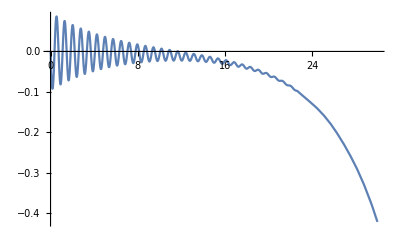

```mathematica
FP = Apart[TF[s]]; 
FP//MatrixForm
IL = InverseLaplaceTransform[FP,s, t] //ComplexExpand;
Plot[IL[[2]][[1]], {t, 0, 30}]
(*https://lpsa.swarthmore.edu/Transient/TransMethTF.html#:~:text=To%20find%20the%20complete%20response,the%20zero%20input%20differential%20equation.*)
```

### Diagrama de Bode

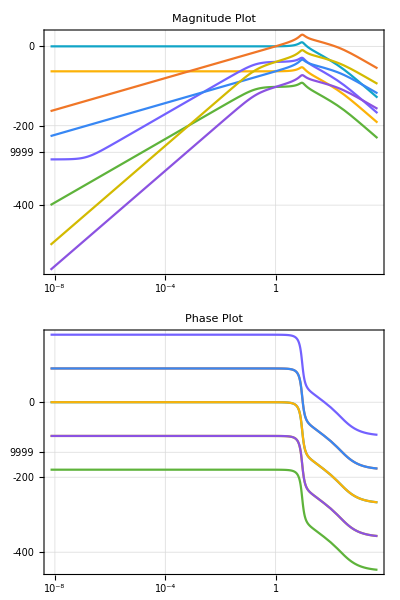

```mathematica
BodePlot[(TF), PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Pós toque

### Modelo incluindo trem de pouso frontal

-Graphics-

```mathematica
Subscript[𝕢, T][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t]};
Subscript[𝕧, T][t_] = {Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
𝕦[t_] = {Subscript[y, ext][t], Subscript[y, ext]'[t]};
𝕪[t_] = {Subscript[q, 2][t], θ[t], Subscript[q, 2]'[t], θ'[t]};
Subscript[v, o] = {0, Subscript[q, 2]'[t], 0};
ω = {0, 0, Subscript[𝕧, T][t][[3]]};
```

Definindo os parâmetros físicos e geométricos do modelo

```mathematica
Subscript[ρ, PO] = {Subscript[D, PO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, PO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor P-O*);
Subscript[ρ, GO] = {Subscript[D, GO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, GO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
Subscript[ρ, FO] = {Subscript[D, FO]*Cos[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], Subscript[D, FO]*Sin[(Subscript[𝕢, T][t][[3]]+ Subscript[Φ, 0])], 0} (*Vetor G-O*);
```

Definindo as forças e momentos externos do modelo

```mathematica
W = {0, -M*g, 0};
Subscript[F, f] = {0, -Subscript[k, Tf]*(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]]+ Subscript[𝕢, T][t][[2]] - Subscript[𝕢, T][t][[4]]), t]), 0};
Subscript[D, ext] = {(-1/2)*Subscript[C, D]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0, 0};
Subscript[L, ext] = {0, (1/2)*Subscript[C, L]*S*ρ*(Subscript[u, longit]+Subscript[u, vento])^2, 0};
Subscript[F, rol] = {Subscript[μ, rol]*(W+Subscript[L, ext])[[2]], 0, 0};
Subscript[M, Tf] = Cross[Subscript[ρ, FO], Subscript[F, f]] //FullSimplify;
Subscript[M, rol]= Cross[Subscript[ρ, GO], Subscript[F, rol]] //FullSimplify;
Subscript[M, aero] = Cross[Subscript[ρ, PO],(Subscript[L, ext]+Subscript[D, ext])] //FullSimplify;
Subscript[M, peso] = Cross[Subscript[ρ, GO], W] //FullSimplify;
Subscript[v, G]= Subscript[v, o] + Cross[ω , Subscript[ρ, GO]] //FullSimplify;
```

### Aplicação do TQMA

O momento angular do corpo do avião em relação a O é, já considerando o movimento como plano:

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[H, o] = M*Cross[Subscript[ρ, GO], Subscript[v, o]] + ω*Subscript[J, oz] //FullSimplify;
M*Cross[Subscript[v, G], Subscript[v, o]] //FullSimplify;
TQMA = (D[Subscript[H, o], t] - M*Cross[Subscript[v, G], Subscript[v, o]]- Subscript[M, rol]- Subscript[M, aero] - Subscript[M, peso] - Subscript[M, Tf])[[3]]//FullSimplify;
```

### Aplicação do TMB no conjunto do trem de pouso (m e mf) e no avião (M)

```mathematica
Subscript[a, G] = D[Subscript[v, o], t] + Cross[D[ω, t], Subscript[ρ, GO]] + Cross[ω, Cross[ω, Subscript[ρ, GO]]];
Subscript[TMB, m] = m*(D[Subscript[𝕧, T][t][[1]], t]) + Subscript[k, r]*(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]) + Subscript[c, r]*(D[(Subscript[𝕢, T][t][[1]] - 𝕦[t][[1]]), t]) - Subscript[k, t]*(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]) - Subscript[c, t]*(D[(Subscript[𝕢, T][t][[2]]-Subscript[𝕢, T][t][[1]]), t]) //FullSimplify;
Subscript[TMB, mf] = Subscript[m, f]*(D[Subscript[𝕧, T][t][[4]], t]) + Subscript[k, rf]*(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]) + Subscript[c, rf]*(D[(Subscript[𝕢, T][t][[4]] - 𝕦[t][[1]]), t]) - Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) - Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) //FullSimplify;
Subscript[TMB, M] = M*Subscript[a, G][[2]] + Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[c, t]*(D[(𝕢[t][[2]]-𝕢[t][[1]]), t]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) + Subscript[c, Tf]*(D[(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]), t]) - Subscript[L, ext][[2]] //FullSimplify;
noequi =  Subscript[k, t]*(𝕢[t][[2]]-𝕢[t][[1]]) + Subscript[k, Tf]*(Subscript[ρ, FO][[2]] + Subscript[q, 2][t] - Subscript[q, 3][t]) //FullSimplify;
```

### O espaço de estados

```mathematica
DINf = {Subscript[TMB, m], Subscript[TMB, M], TQMA, Subscript[TMB, mf]};

Solf[t_] = Flatten @ Solve[
	(# == 0)& /@ DINf,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
𝕩f[t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Ff = (𝕩f'[t] /.Solf[t]); 
Ff //FullSimplify //MatrixForm
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-4 g M Cos[Φ_0+θ[t]]^2+Sin[2 (Φ_0+θ[t])] (2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol)+M D_GO (S ρ (Sin[2 (Φ_0+θ[t])] C_D+2 Cos[Φ_0+θ[t]]^2 C_L) D_PO (u_longit+u_vento)^2-4 Sin[Φ_0+θ[t]] J_oz θ'[t]^2-4 Cos[Φ_0+θ[t]]^2 D_FO^2 (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+4 Cos[Φ_0+θ[t]]^2 D_FO (k_Tf (-q_2[t]+q_3[t])+c_Tf (-q_2'[t]+q_3'[t])))+2 J_oz (-S ρ C_L (u_longit+u_vento)^2+2 D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])-2 (k_t (q_1[t]-q_2[t])+k_Tf (-q_2[t]+q_3[t])+c_t (q_1'[t]-q_2'[t])+c_Tf (-q_2'[t]+q_3'[t]))))/(4 M (M Cos[Φ_0+θ[t]]^2 D_GO^2-J_oz))
(-S ρ Sec[Φ_0+θ[t]] C_L D_PO (u_longit+u_vento)^2+2 D_FO^2 k_Tf Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit^2 Tan[Φ_0+θ[t]]-2 S ρ Sec[Φ_0+θ[t]] C_D D_PO u_longit u_vento Tan[Φ_0+θ[t]]-S ρ Sec[Φ_0+θ[t]] C_D D_PO u_vento^2 Tan[Φ_0+θ[t]]+2 Sec[Φ_0+θ[t]] D_FO k_Tf q_2[t]-2 Sec[Φ_0+θ[t]] D_FO k_Tf q_3[t]+2 c_Tf D_FO^2 θ'[t]+2 M D_GO^2 Tan[Φ_0+θ[t]] θ'[t]^2+2 Sec[Φ_0+θ[t]] c_Tf D_FO q_2'[t]+D_GO (S ρ Sec[Φ_0+θ[t]] C_L (u_longit+u_vento)^2 (1+μ_rol Tan[Φ_0+θ[t]])-2 (D_FO (k_Tf Tan[Φ_0+θ[t]]+c_Tf θ'[t])+Sec[Φ_0+θ[t]] (-g M+g M μ_rol Tan[Φ_0+θ[t]]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))-2 Sec[Φ_0+θ[t]] c_Tf D_FO q_3'[t])/(2 M D_GO^2-2 Sec[Φ_0+θ[t]]^2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (Sin[Φ_0+θ[t]] k_Tf+Cos[Φ_0+θ[t]] c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

### Linearização

As variáveis são todas incrementais, assim  será linearizada em torno de 0, assim como   e  tomando  = 0 .

```mathematica
POSequif = {Subscript[q, 1][t] -> 0 , Subscript[q, 2][t] -> 0, θ[t] -> - Subscript[Φ, 0], Subscript[q, 3][t] -> 0}; (*Posição de equilíbrio trivial do sistema*)
DINflin = Linearize[DINf, POSequif]; (*ELS -> Equação dinâmica não-linear*)

Solflin[t_] = Flatten @ Solve[
	(# == 0)& /@ DINflin,
	Subscript[𝕧, T]'[t]
	] // Collect[#, Subscript[𝕧, T][t], FullSimplify]&;
	
Subscript[𝕩f, lin][t_] = {Subscript[q, 1][t], Subscript[q, 2][t], θ[t], Subscript[q, 3][t], Subscript[q, 1]'[t], Subscript[q, 2]'[t], θ'[t], Subscript[q, 3]'[t]};
Subscript[Ff, lin] = (Subscript[𝕩f, lin]'[t] /.Solflin[t]);
Subscript[Ff, lin] //TrigReduce //FullSimplify //MatrixForm 
(*aquiiiiiiiiiiiiiiiiiiiiiiiii*)
```

(q_1'[t]
q_2'[t]
θ'[t]
q_3'[t]
(k_t (-q_1[t]+q_2[t])+k_r (-q_1[t]+y_ext[t])+c_t (-q_1'[t]+q_2'[t])+c_r (-q_1'[t]+y_ext'[t]))/m
(M D_GO^2 (-2 g M+(2 g M-S ρ C_L (u_longit+u_vento)^2) μ_rol θ[t])+M D_GO (S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])-2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))-J_oz (S ρ C_L (u_longit+u_vento)^2-2 (k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t]))))/(2 M (M D_GO^2-J_oz))
(-S ρ D_PO (u_longit+u_vento)^2 (C_L+C_D θ[t])+D_GO (S ρ C_L (u_longit+u_vento)^2 (1+μ_rol θ[t])-2 (-g M+g M μ_rol θ[t]+k_t (-q_1[t]+q_2[t])+k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_t (-q_1'[t]+q_2'[t])+c_Tf (q_2'[t]-q_3'[t])))+2 D_FO (k_Tf (q_2[t]-q_3[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])))/(2 M D_GO^2-2 J_oz)
(k_Tf (q_2[t]-q_3[t])+k_rf (-q_3[t]+y_ext[t])+D_FO (k_Tf θ[t]+c_Tf θ'[t])+c_Tf (q_2'[t]-q_3'[t])+c_rf (-q_3'[t]+y_ext'[t]))/m_f)

```mathematica
𝔸f = CoefficientArrays[Subscript[Ff, lin], Subscript[𝕩f, lin][t]][[2]]//Normal; 
𝔸f //FullSimplify//MatrixForm;

𝔹f = CoefficientArrays[Subscript[Ff, lin], 𝕦[t]][[2]]//Normal; 
𝔹f //MatrixForm;

ℂf = { {0,1,0,0,0,0,0,0}, {0,0,1,0,0,0,0,0}, {0,0,0,0,0,1,0,0}, {0,0,0,0,0,0,1,0}};
ℂf //MatrixForm;

𝔻f = {{0,0},{0,0},{0,0},{0,0}};
𝔻f //MatrixForm;
 
𝕩f[t] //MatrixForm ;
𝕩f'[t] //MatrixForm;
𝕦[t] //MatrixForm ;
𝕪[t] //MatrixForm ;
```

### Substituindo os valores numéricos

```mathematica
rep2 = {Subscript[D, FO]->18.2, Subscript[k, Tf]->11486800/2, Subscript[c, Tf]-> 1021960/2, Subscript[k, rf]-> 13600000/4, Subscript[c, rf]-> 9700/4, Subscript[m, f]->1000};
SS = StateSpaceModel[{𝔸f/.(rep2)/.(rep)/.(Subscript[u, longit]->280/3.6)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), 𝔹f/.(rep2)/.(rep)/.(Subscript[u, longit]->280/3.6)/.(Subscript[Φ, 0] -> 13*3.14/180)/.(Subscript[u, vento]->0)/.(Subscript[C, pav]->1), ℂf, 𝔻f}]
```

0000100000000001000000000010000000000100-62717/1028717/1000-51583/20025549/10000340097/40133.914-186.881-964.0552.967511.9141-16.6265-85.76614.7124200-1.5373-4.05289-101.7235.5902-0.136771-0.360579-9.051760.4973500028717/5104530.-45717/5025549/509299.84-102681/200340097/400100000000001000000000000100000000001000StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2$CellContext`stname3$CellContext`stname4$CellContext`stname5$CellContext`stname6$CellContext`stname7$CellContext`stname8Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic2481FalseFalseFalseAutomaticNoneAutomatic

```mathematica
TFf = TransferFunctionModel[SS, s]
```

```mathematica
(1.745282603075172*^11+3.118329179482092*^10 s+6.747824583214443*^9 s^2+7.611950276458383*^8 s^3+2.597126294092075*^7 s^4+56530.10003328137 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(1.2447971507229614*^8+2.224102429483795*^7 s+4.812786651264191*^6 s^2+542911.1594238281 s^3+18523.621362268925 s^4+40.31926252413541 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.0001220703125+7.141307544117928*^7 s^2+8.572115094852805*^6 s^3+211166.63687618077 s^4+1225.9669270208105 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000030517578125+50934.32586860657 s^2+6113.935030817985 s^3+150.61149835586548 s^4+0.8744028815999627 s^5)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(56530.10003328111 (3.0873509900878775*^6 s+551622.7952270083 s^2+119366.93158585922 s^3+13465.304805717626 s^4+459.42361548326704 s^5+s^6))/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(40.319262523757054 (3.087350990086266*^6 s+551622.7952267507 s^2+119366.93158580044 s^3+13465.304805710715 s^4+459.4236154830451 s^5+s^6))/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000034332275390625 s-1.9073486328125*^-6 s^2+7.141307544117641*^7 s^3+8.572115094852641*^6 s^4+211166.6368761873 s^5+1225.9669270210143 s^6)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)(-0.000034332275390625 s-1.9073486328125*^-6 s^2+50934.325866103165 s^3+6113.93503087759 s^4+150.6114983614534 s^5+0.8744028817745857 s^6)/(1.7452826030751727*^11+3.130777150989321*^10 s+8.98981965442321*^9 s^2+1.0588565983881725*^9 s^3+9.496358003733464*^7 s^4+5.996756780701021*^6 s^5+157967.13531263833 s^6+796.9982639334324 s^7+s^8)TransferFunctionModelFalseFalseFalseFalse$FailedControl`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$#$CellContext`s241.745282603075172e111.2447971507229614e8-0.0001220703125-0.00003051757812556530.1000332811140.319262523757054-0.000034332275390625-0.0000343322753906251.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111.7452826030751727e111FalseFalseFalseAutomaticNoneAutomatic
```

```mathematica
TransferFunctionPoles[TFf] [[3]][[1]] //MatrixForm
TransferFunctionPoles[TFf] [[4]][[1]] //MatrixForm
```

(-509.193
-243.925
-22.7529
-16.2178
-1.87554-10.6961 ⅈ
-1.87554+10.6961 ⅈ
-0.579665-5.65298 ⅈ
-0.579665+5.65298 ⅈ)

(-509.193
-243.925
-22.7529
-16.2178
-1.87554-10.6961 ⅈ
-1.87554+10.6961 ⅈ
-0.579665-5.65298 ⅈ
-0.579665+5.65298 ⅈ)

```mathematica
TransferFunctionZeros[TFf] //MatrixForm
```

({-428.653,-18.3811,-11.24,-0.574636-5.87632 ⅈ,-0.574636+5.87632 ⅈ} | {-428.653,-18.3811,-11.24,-0.574636-5.87632 ⅈ,-0.574636+5.87632 ⅈ}
{-116.533,-44.4717,-11.24,-1.30742×10^-6,1.30742×10^-6} | {-116.533,-44.4717,-11.24,-0.0000244777,0.0000244776}
{-428.653,-18.3811,-11.24,-0.574636-5.87632 ⅈ,-0.574636+5.87632 ⅈ,0} | {-428.653,-18.3811,-11.24,-0.574636-5.87632 ⅈ,-0.574636+5.87632 ⅈ,0}
{-116.533,-44.4717,-11.24,-6.93366×10^-7,0,6.93366×10^-7} | {-116.533,-44.4717,-11.24,-0.0000259625,0,0.0000259624})

### Diagrama de Bode

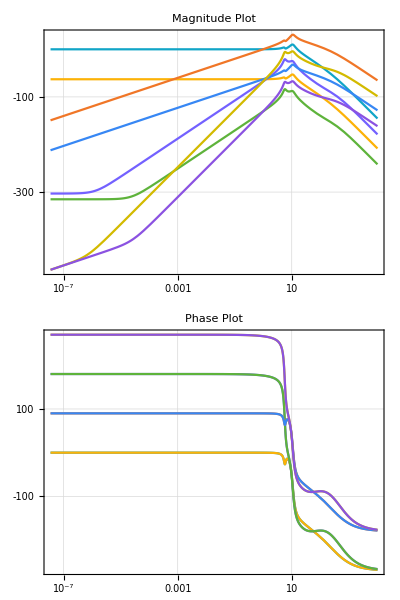

```mathematica
BodePlot[TFf, PlotTheme->"Scientific", GridLines->Automatic, PlotStyle->100, PlotLabel->{"Magnitude Plot","Phase Plot"}]
```

## Exportando o aquivo .m do espaço de estados

Para exportar outro espaço de estados, basta substituir o argumento da 4 linha da terceira célula de código por:
WriteString[fileD, (#/.(({ii_}→vv_):>(StringReplace[StringReplace[ToString @ StringForm[“    ``;”, (vv /. crule //CForm)], csqrule], csorule]<>”\n”)))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕩’[t]/.NOMEDASOLUCAO[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));

```mathematica
(*Unprotect[Power];
Format[Power[a_,n_Integer],CForm]:=Distribute[ConstantArray[Hold[a],n],Hold,List,HoldForm,Times]
Protect[Power];*)
```

```mathematica
(*crule = MapThread[#1->#2&, {#, x/@((Range[Length@#]))}& @ 𝕩[t]];
csorule = {"Cos"->"cos", "Sin"->"sin", "Tan"->"tan", "Sec"->"sec"};
csqrule = {};*)
```

```mathematica
(*fileD = OpenWrite["trab_esp_linearizado0.m"];
(*WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["dy(``) = ``;", ii, (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(𝕪'[t]/.EOM[t])], -1]));*)
WriteString[fileD, (#/.(({ii_}->vv_):>(StringReplace[StringReplace[ToString @ StringForm["    ``;", (vv /. crule //CForm)], csqrule], csorule]<>"\n")))]&/@ (Normal@(Select[#,Not @(NumericQ[#])&]&@Association@Delete[ArrayRules@SparseArray[(Subscript[𝕩f, lin]'[t]/.Solflin[t](*Join[𝕣𝕢[t], EOM2[t]]*))], -1]));
WriteString[fileD, "\n"];
Close[fileD];*)
```